Scientific

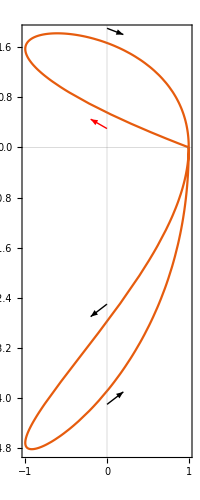

../figure/two-curve.png

```mathematica
SetDirectory[NotebookDirectory[]];
$PlotTheme="Scientific"
plot=ParametricPlot[{Cos[2*t],t*Sin[t]},{t,0,2*Pi},Epilog->{{Red,Arrow[{{0,0.3},{-0.2,0.45}}]},Arrow[{{0,1.9},{0.2,1.8}}],Arrow[{{0,-2.5},{-0.2,-2.7}}],Arrow[{{0,-4.1},{0.2,-3.9}}]}]
Export["../figure/two-curve.png",plot]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["..figure/two-curve.png"]]]
```

```mathematica
Epilog
```

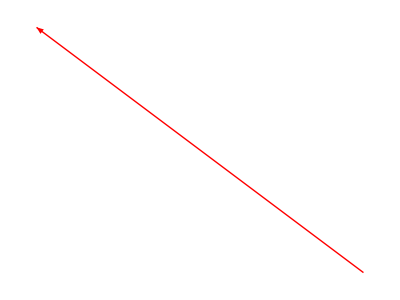

```mathematica
Plot
```